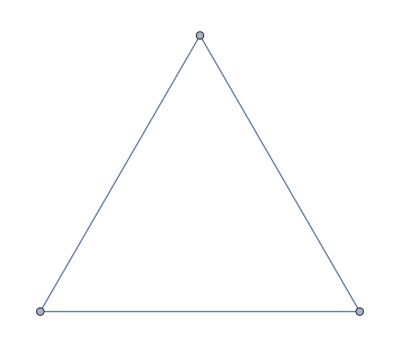

```mathematica
g=Graph[{1<->2,1<->3,2<->3}]
```

```mathematica
FindFullFormula[g]
```

{v1x2}

```mathematica
FormulaLevels[{v1x2x3,v1x23,v13x2}]
```

{{2,2},{3,1}}

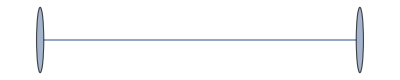

```mathematica
g=Graph[{1<->2}]
```

```mathematica
Block[{h=g,next=3},
For[next=3,next<8,next++,
h=VertexAdd[h,next];
Print[next<->Map[Last,FormulaLevels[FindFullFormula[h]]]]
];
]
```

3<->{2,1}

4<->{4,5,1}

5<->{8,19,9,1}

6<->{16,65,55,14,1}

7<->{32,211,285,125,20,1}

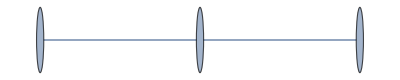

```mathematica
g=Graph[{1<->2,1<->3}]
```

```mathematica
Block[{h=g,next=3},
For[next=4,next<8,next++,
h=VertexAdd[h,next];
Print[next<->Map[Last,FormulaLevels[FindFullFormula[h]]]]
];
]
```

4<->{2,4,1}

5<->{4,14,8,1}

6<->{8,46,46,13,1}

7<->{16,146,230,111,19,1}

```mathematica
g=Graph[{1<->2,1<->3,2<->3}]
```

-Graphics-

```mathematica
Block[{h=g,next=3},
For[next=4,next<8,next++,
h=VertexAdd[h,next];
Print[next<->Map[Last,FormulaLevels[FindFullFormula[h]]]]
];
]
```

4<->{3,1}

5<->{9,7,1}

6<->{27,37,12,1}

7<->{81,175,97,18,1}

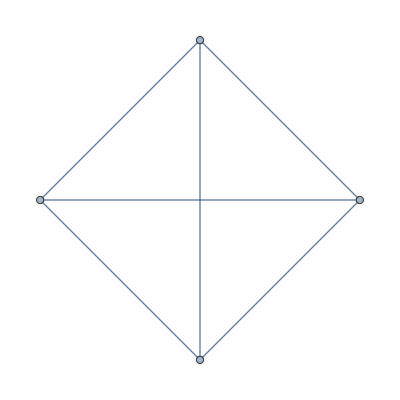

```mathematica
g=Graph[{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4}]
```

```mathematica
Block[{h=g,next=3},
For[next=5,next<8,next++,
h=VertexAdd[h,next];
Print[next<->Map[Last,FormulaLevels[FindFullFormula[h]]]]
];
]
```

5<->{4,1}

6<->{16,9,1}

7<->{64,61,15,1}

```mathematica
t[n_,k_]:=StirlingS2[n,k]-6*StirlingS2[n-1,k]+11*StirlingS2[n-2,k]-6*StirlingS2[n-3,k];TableForm[Table[t[n,k],{n,4,13},{k,4,n}]]
```

1 |  |  |  |  |  |  |  |  | 
4 | 1 |  |  |  |  |  |  |  | 
16 | 9 | 1 |  |  |  |  |  |  | 
64 | 61 | 15 | 1 |  |  |  |  |  | 
256 | 369 | 151 | 22 | 1 |  |  |  |  | 
1024 | 2101 | 1275 | 305 | 30 | 1 |  |  |  | 
4096 | 11529 | 9751 | 3410 | 545 | 39 | 1 |  |  | 
16384 | 61741 | 70035 | 33621 | 7770 | 896 | 49 | 1 |  | 
65536 | 325089 | 481951 | 305382 | 95781 | 15834 | 1386 | 60 | 1 | 
262144 | 1690981 | 3216795 | 2619625 | 1071630 | 238287 | 29694 | 2046 | 72 | 1